# Skeleton-based Analysis of Melt Network

## Functions

```mathematica
Clear["Global`*"];
```

readSkel[path] reads .ply skeleton file as a table and returns points, lines and radius:

```mathematica
readSkel:= Function[path, 
	rawData = Import[path,"Table"];
	numOfPoints = rawData⟦3,3⟧;
	numOfEdges = rawData⟦9,3⟧;
	dataTable = rawData⟦15;;,;;⟧;
	
	burnTime = dataTable⟦;;numOfPoints,1⟧;
	Points = dataTable⟦;;numOfPoints,3;;5⟧;
	Lines = dataTable⟦numOfPoints+1;;⟧ + 1;
	Radius = dataTable⟦;;numOfPoints,2⟧;
	{Points,Lines,Radius,burnTime}
]
```

getRange[list] returns the range(min and max value) of elements in the list:

```mathematica
getRange:=Function[list,
	min = Min[list];
	max = Max[list];
	{min, max}]
```

move[from, to] add an offset to list from based on the distance between center of range2 and range1:

```mathematica
move:=Function[{from,to},
	range1 = getRange[from];
	range2 = getRange[to];
	offset = (range2⟦1⟧ + range2⟦2⟧-range1⟦1⟧ - range1⟦2⟧)/2;
	res = from + offset;
	res]
```

coordsAlign[coords1, coords2] add offsets to each dimension of coords1 so that coords1 is aligned with coords2. coords1, coords2: N by 3(x,y,z)

```mathematica
coordsAlign:=Function[{coords1,coords2},
	newX = move[coords1⟦;;,1⟧,coords2⟦;;,1⟧];
	newY = move[coords1⟦;;,2⟧,coords2⟦;;,2⟧];
	newZ = move[coords1⟦;;,3⟧,coords2⟦;;,3⟧];
	newCoords1 = {newX,newY,newZ};
	Transpose[newCoords1]]
```

linesToGraph[lines] construct a graph based on the lines

```mathematica
linesToGraph:=Function[{lines},
	graph=Graph[Table[lines⟦i,1⟧<->lines⟦i,2⟧,{i,1,Dimensions[lines]⟦1⟧}]]
]
```

getJunctions[graph] collect all junction nodes(degree >= 3) and their degree from a graph

```mathematica
getJunctions:=Function[{graph},
	ans={};
	For[i=1,i≤VertexCount[graph],i++,
	degree = VertexDegree[graph,i];
	If[degree>2,AppendTo[ans,{i,degree}]]];
	ans
]
```

InitJG[points, lines, radius] generates a list of junctions and a simplified graph based on these junctions
	Inputs: 
		points: a list of all points in skeleton
		lines: a list of all lines in skeleton
		radius: a list of radius of each point in skeleton
	Returns:
		junctionDataTable: a list of all basic junctions {identifier, degree, cluster, coordinate, radius}
		simplifiedG: a simplified graph which eliminates all vertices with degree of 2

```mathematica
initJG:= Function[{points, lines, radius,burntime},
	skelGraph = linesToGraph[lines];
	Print["Initial graph built!"];
	simplifiedG = simplifyGraph[skelGraph];
	Print["simplified graph done!"];
	junctions = getJunctions[skelGraph];
	junctionsDataTable = Table[{junctions⟦i,1⟧,junctions⟦i,2⟧,{{junctions⟦i,1⟧,points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧}},points⟦junctions⟦i,1⟧,;;⟧,radius⟦junctions⟦i,1⟧⟧,burntime⟦junctions⟦i,1⟧⟧,EdgeList[simplifiedG, junctions⟦i,1⟧<->_]},{i,Dimensions[junctions]⟦1⟧}];	
	junctionsDataTable = Select[junctionsDataTable,#⟦6⟧ > 1 &];
	Print["Basic junctions computed!"];
	{junctionsDataTable, simplifiedG}
]
```

```mathematica
a=Graph[{1<->2,1<->1}];
EdgeList[a,1<->_]
AdjacencyMatrix[a]//MatrixForm
```

{1<->2,1<->1}

(1 | 1
1 | 0)

```mathematica
computeAngle:=Function[{apex,point1,point2},
	vec1=point1-apex;
	vec2=point2-apex;
	If[Norm[vec1]*Norm[vec2] == 0, 
		angle = 0,
		cosValue=vec1.vec2/(Norm[vec1]*Norm[vec2]);
		angle = ArcCos[cosValue]/(2*Pi) * 360;
	];
	angle
]
```

```mathematica
computeStdAngle:=Function[d,
	points = SpherePoints[d];
	minAngle = 180;
	For[i=1, i≤Length[points] - 1,i++,
		For[j =i+1, j≤ Length[points], j++,
			theAngle = computeAngle[{0,0,0},points⟦i⟧,points⟦j⟧];
			minAngle = Min[theAngle, minAngle]; 
		]
	];
	minAngle
]
```

```mathematica
angleScore:=Function[{simplifiedG, allPoints, c1, c2, d, stdAngle},
	neighbors=AdjacencyList[simplifiedG,c1⟦1⟧];
	neighbors = Select[neighbors, #≠c2⟦1⟧ && #≠c1⟦1⟧ &];
	n=Length[neighbors];
	aScore = -100;
	For[i=1,i≤n-1,i++,
		point1=allPoints⟦neighbors⟦i⟧,;;⟧;
		For[j=i+1,j≤n,j++,
			point2=allPoints⟦neighbors⟦j⟧,;;⟧;
			theAngle=computeAngle[c1⟦4⟧,point1,point2];
			aScore = Max[aScore, Abs[theAngle - stdAngle] / (10+d*5)];
		];
	];
	aScore
]
```

```mathematica
clusterAngleScore:= Function[{simplifiedG,allPoints, c1, c2, d},
	stdAngle = computeStdAngle[d];
	aScore1 = angleScore[simplifiedG, allPoints, c1, c2, d, stdAngle];
	aScore2 = angleScore[simplifiedG, allPoints, c2, c1, d, stdAngle];
	worstScore = Max[aScore1, aScore2];
	worstScore
]
```

distanceScore[ball1, ball2] computes the score which tell whether the two balls should be merged
	ball1: {identifier, {x1,y1,z1}, r1} 
	ball2: {identifier, {x2,y2,z2}, r2}

```mathematica
distanceScore := Function[{ball1, ball2},
	r1 = Max[ball1⟦3⟧,ball2⟦3⟧];
	r2 = Min[ball1⟦3⟧,ball2⟦3⟧];
	d = EuclideanDistance[ball1⟦2⟧, ball2⟦2⟧];
	score = If[r2==0, -r1+d,(-r1 - r2 + d)/(2*r2)];
	score
]
```

clusterDistanceScore[simplifiedG,c1,c2] computes the distance score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the worst distance score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterDistanceScore:= Function[{simplifiedG,c1,c2},
	worstScore = -100;
	ballList1 = c1⟦3⟧;
	ballList2 = c2⟦3⟧;
	For[i=1, i≤Length[ballList1],i++,
		For[j=1, j≤Length[ballList2],j++,
			If[EdgeQ[simplifiedG,ballList1⟦i,1⟧<->ballList2⟦j,1⟧],
				worstScore = Max[worstScore, distanceScore[ballList1⟦i⟧, ballList2⟦j⟧]];
			]
		]
	];
	worstScore
]
```

clusterMergeScore[c1,c2] computes the worst score between cluster c1 and cluster c2
Inputs:
	c1, c2: a merged junction {identifier, degree, cluster, coordinate, radius}
Return:
	worstScore: the minimum score among all scores between each ball in  c1 and each ball in c2

```mathematica
clusterMergeScore:= Function[{simplifiedG,,initSimpleG,allPoints,c1,c2},
	dScore = clusterDistanceScore[initSimpleG, c1, c2];
	d = c1⟦2⟧ + c2⟦2⟧ - innerDegree * 2;
	aScore = clusterAngleScore[simplifiedG,allPoints,c1,c2,d];
	totalScore=(d-1)/d*dScore + 1/d*aScore;
	{dScore, aScore, totalScore}
]
```

```mathematica
isMergable:=Function[{dScore, totalScore},
	If[dScore ≤ 1 && totalScore ≤ 1, 
		True, 
		False
	]
]
```

```mathematica
deleteNode := Function[{graph, v},
	resGraph = graph;
	If[VertexDegree[graph, v] ≠ 2, Throw[resGraph]];
	
	neighbors = AdjacencyList[resGraph,v];
	v1 = neighbors⟦1⟧;
	v2 = If[Length[neighbors] == 2,neighbors⟦2⟧, neighbors⟦1⟧];
	
	resGraph = VertexDelete[resGraph, v];
	resGraph = EdgeAdd[resGraph,v1<->v2];
	resGraph
]
```

```mathematica
simplifyGraph := Function[{skelGraph},
	g = skelGraph;
	nodesDeg2 = Pick[VertexList[g], VertexDegree[g], 2];
	
	While[Length[nodesDeg2] > 0,
		g = Catch[deleteNode[g, nodesDeg2⟦1⟧]];
		nodesDeg2 = Drop[nodesDeg2,1];
		If[Mod[Length[nodesDeg2],500]==0,Print[Length[nodesDeg2]]];
	];
	g
]
```

smallestCircumBall[ball1,ball2] computes the smallest circumscribe ball of ball1 and ball2
Inputs:
	ball: {identifier, degree, cluster, coordinate, radius}
Return:
	{c,r}: c is the center and r is the radius

```mathematica
smallestCircumBall:=Function[{ball1,ball2},
	c1 = ball1⟦4⟧;
	r1 = ball1⟦5⟧;
	c2 = ball2⟦4⟧;
	r2 = ball2⟦5⟧;
	
	d = EuclideanDistance[c1, c2];
	
	If[d == 0, Throw[{c1,Max[r1,r2]}]];
	
	t1 = r1/d;
	t2 = -r1/d;
	t3 = 1+r2/d;
	t4 = 1-r2/d;
	tmax = Max[t1,t2,t3,t4];
	tmin = Min[t1,t2,t3,t4];
	c3 = c1 + (tmax+tmin)/2*(c2-c1);
	r3 = (Abs[tmax]+Abs[tmin])/2*d;
	{c3,r3}
]
```

mergeJunctions[ball1,ball2] merges ball1 and ball2
inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph showing connectivity relationship of junctions
	ball: {identifier, degree, cluster, coordinate, radius}
return: 
	a list consisting of an updated junction list and an updated graph

```mathematica
mergeJunctions:= Function[{junctionList, graph, ball1, ball2},
	newJunctionList = junctionList;

	v1 = ball1⟦1⟧;
	v2 = ball2⟦1⟧;
	innerEdges = EdgeList[graph,v1<->v2];
	
	g = EdgeDelete[graph, innerEdges];
	g = VertexReplace[g,{v2->v1}];
	
	newDegree = VertexDegree[g,v1];
	
	{c3,r3}= Catch[smallestCircumBall[ball1,ball2]];
	newclusterList = Join[ball1⟦3⟧,ball2⟦3⟧];
	
	newClusterIDs=newclusterList⟦;;,1⟧;
	newExternalEdgeList=Join[ball1⟦7⟧,ball2⟦7⟧];
	newExternalEdgeList=Select[newExternalEdgeList, Xor[MemberQ[newClusterIDs, #⟦1⟧],MemberQ[newClusterIDs, #⟦2⟧]] || #⟦1⟧==#⟦2⟧ &];
	
	If[Length[newExternalEdgeList]≠newDegree, 
		Print["newDegree:",newDegree];
		Print["newExternalEdgeList:",newExternalEdgeList];
		Print[ball1];
		Print[ball2];
	];
	
	newBall = {v1,newDegree,newclusterList,c3,r3,{},newExternalEdgeList};
	
	newJunctionList = DeleteCases[newJunctionList,ball1];
	newJunctionList = DeleteCases[newJunctionList,ball2];
	newJunctionList = AppendTo[newJunctionList,newBall];

	{newJunctionList, g}
]
```

```mathematica
updateEdgeListByID:=Function[{edgeList, oldID, newID},
	newEdgeList = edgeList;
	For[i=1, i≤Length[edgeList], ++i,
		edge=edgeList⟦i⟧;
		If[edge⟦1⟧==oldID, edge⟦1⟧=newID];
		If[edge⟦2⟧==oldID, edge⟦2⟧=newID];
		newEdgeList⟦i⟧=edge;
	];
	newEdgeList
]
```

computeCN[junctionList, graph] merges the junctions and return the junction list and graph after merging
Inputs:
	junctionList: {identifier, degree, cluster, coordinate, radius}
		cluster is a list of nodes {identifier,{x,y,z},radius}
	graph: the simplified graph before merging
Returns:
	J: merged junctions
	G: the graph after merging

```mathematica
computeCN:=Function[{junctionList,initSimpleG,allPoints},
	J = junctionList;
	G = initSimpleG;
	threshold = 1;
	candidateEdgeList = {};
	While[True,
		minScore = threshold+100;
		tgt1 = {};
		tgt2 = {};
		
		edges = EdgeList[G];
		Do[
			j1 = edge⟦1⟧;
			j2 = edge⟦2⟧;
			
			If[j1 == j2, Continue[]];
			
			c1 = Select[J,#⟦1⟧ == j1 &];
			c2 = Select[J,#⟦1⟧ == j2 &];

			If[c1 == {} || c2 == {}, Continue[]];
			
			c1 = c1⟦1⟧;
			c2 = c2⟦1⟧;
	
			(*dScore=clusterDistanceScore[initSimpleG,c1,c2];
			aScore=clusterAngleScore[G,allPoints,c1,c2];*)
			{dScore,aScore,totalScore}=clusterMergeScore[G,,initSimpleG,allPoints,c1,c2];
			If[isMergable[dScore, totalScore] && !MemberQ[candidateEdgeList⟦;;,1⟧, j1<->j2] && !MemberQ[candidateEdgeList⟦;;,1⟧, j2<->j1],
				AppendTo[candidateEdgeList, {edge, totalScore, aScore}];
			];
		,{edge,edges}];
		
		If[Length[candidateEdgeList] == 0, Break[]];
		candidateEdgeList = Sort[candidateEdgeList, #1⟦2⟧ < #2⟦2⟧ &];
		Print[candidateEdgeList⟦;;,2;;3⟧];
		While[Length[candidateEdgeList]>0,
			Print[Length[candidateEdgeList]];
			
			candidateEdge = candidateEdgeList⟦1,1⟧;
			tgt1 = candidateEdge⟦1⟧;
			tgt2 = candidateEdge⟦2⟧;
			ball1 = Select[J,#⟦1⟧ == tgt1 &]⟦1⟧;
			ball2 = Select[J,#⟦1⟧ == tgt2 &]⟦1⟧;
			{J,G} = mergeJunctions[J,G,ball1,ball2];

			candidateEdgeList⟦;;,1⟧=updateEdgeListByID[candidateEdgeList⟦;;,1⟧,ball2⟦1⟧, ball1⟦1⟧];	
			candidateEdgeList=Drop[candidateEdgeList,1];		
		];
	];
	{J,G}
]
```

```mathematica
degreeColor:=Function[d,
	Switch[d,
		2, Black,
		3, Brown,
		4, Yellow,
		5, Magenta,
		6, Cyan,
		7, Red,
		_, Blue
	]
]
```

## Function Test

### test data

test getRange[list], move[from, to]

```mathematica
list1 = {1,2.5,3.7,4}; list2 = {5,6,7,8};
list1 = move[list1,list2]
```

{5,6.5,7.7,8}

test coordsAlign[coords1, coords2]

```mathematica
coords1={{0,0,0},{0,1,0},{0,0,1},{0,1,1},{1,0,0},{1,1,0},{1,0,1},{1,1,1}};
coords2={{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}};
coords3=coordsAlign[coords1,coords2]

a = Graphics3D[{
	Red,Point[coords1],
	Green,Point[coords2],
	Red,Opacity[0.3],Ball[coords3,0.1]
}];
Show[a]
```

{{2,1,4},{2,2,4},{2,1,5},{2,2,5},{3,1,4},{3,2,4},{3,1,5},{3,2,5}}

-Graphics3D-

test linesToGraph[lines] and getJunctions[graph]

```mathematica
testLines = {{1,2},{2,3},{1,4},{4,3},{1,3},{3,1}};
(*testLines = {{1,2},{1,2}};*)
g = linesToGraph[testLines]
```

-Graphics-

test deleteNode[graph, v], simplifyGraph[graph]

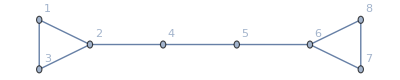

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
(*s = simplifyGraph[g];
GraphPlot3D[s]*)
```

```mathematica
EdgeQ[g,5<->4]
```

True

test mergeScore

```mathematica
ball1 = {{1,2,3},2};
ball2 = {{4,5,6},6};
mergeScore[ball1, ball2]
```

mergeScore[{{1,2,3},2},{{4,5,6},6}]

test simplifyGraph

```mathematica
g = Graph[{1<-> 2, 2 <-> 3, 3 <-> 1,2<->4,4<->5,5<->6,6<->7,7<->8,8<->6}, VertexLabels -> "Name"]
h = simplifyGraph[g];
GraphPlot3D[h]
```

-Graphics-

0

-Graphics3D-

test smallestCircumBall

```mathematica
c1 = {0,0,0};
r1 = 1;
c2 = {0.1,0.5,0.6};
r2 = 0.4;
{c3,r3} = smallestCircumBall[{1,2,c1,r1},{1,2,c2,r2}]

a1 = Ball[c1,r1];
a2 = Ball[c2,r2];
a3 = Ball[c3,r3];

Graphics3D[{
	Opacity[0.5],
	Green,a1,
	Blue,a2,
	Red,a3}]
```

Part::partw: Part 5 of {1,2,{0,0,0},1} does not exist.

Part::partw: Part 5 of {1,2,{0.1,0.5,0.6},0.4} does not exist.

{1-0.3 (Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]+Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]),0.3 (Abs[Max[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]]+Abs[Min[-1.66667 {1,2,{0,0,0},1}⟦5⟧,1.66667 {1,2,{0,0,0},1}⟦5⟧,1-1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧,1+1.66667 {1,2,{0.1,0.5,0.6},0.4}⟦5⟧]])}

```mathematica
a=Graph[{1<->2,1<->2,1<->3,4<->2}]
```

-Graphics-

```mathematica
b=EdgeList[a,1<->_]
```

{1<->2,1<->2,1<->3}

```mathematica
c=EdgeList[a,2<->_]
```

{1<->2,1<->2,4<->2}

```mathematica
d=Join[b,c]
```

{1<->2,1<->2,1<->3,1<->2,1<->2,4<->2}

```mathematica
e={1,2};
```

```mathematica
Select[d, (MemberQ[e, #⟦1⟧]&&!MemberQ[e, #⟦2⟧])||(!MemberQ[e, #⟦1⟧]&&MemberQ[e, #⟦2⟧]) &]
```

{1<->3,4<->2}

## Code

### Set working directory

```mathematica
SetDirectory["D:\\MyLearning\\proj\\Skeleton_Analysis_of_Melt_Network"];
```

### Excel Data

```mathematica
groundTruthTable = Import["data\\scoba12.xlsx"];
```

```mathematica
groundTruthTable = groundTruthTable[[1,;;,;;]];
trueJunctions = groundTruthTable[[;;,{4,5,6,10,19}]];
```

### scoba12_small

#### Medial Axis

```mathematica
maRawData = Import["scoba12_small.ply","Table"];
maTable = maRawData⟦15;;,;;⟧;
maPoints = maTable⟦;;86117,;;⟧;
maPoints = coordsAlign[maPoints,skelPoints];
maPolygons = maTable⟦363203;;,10;;12⟧ + 1;
```

```mathematica
polygonInCoords = Table[{Blue,Polygon[{maPoints⟦maPolygon⟦1⟧⟧,maPoints⟦maPolygon⟦2⟧⟧,maPoints⟦maPolygon⟦3⟧⟧}]},{maPolygon,maPolygons}];
```

#### Skeleton & Junctions

```mathematica
{thepoints,thelines,theradius,burnTime}=readSkel["scoba12_small_skel.ply"];
```

```mathematica
{theJ,theG}=initJG[thepoints,thelines,theradius,burnTime];
```

Initial graph built!

11500

11000

10500

10000

9500

9000

8500

8000

7500

7000

6500

6000

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

Basic junctions computed!

```mathematica
{theJres,theGres}=computeCN[theJ,theG,thepoints];
```

{{-49.5922,-100},{-25.4271,-100},{-25.365,-100},{-24.7835,-100},{-24.7821,-100},{-24.6951,-100},{-24.6414,-100},{-24.4194,-100},{-0.420187,0.752674},{-0.419356,0.84568},{-0.384275,1.4629},{-0.380571,0.290616},{-0.281491,1.25328},{-0.280479,1.0624},{-0.209321,1.15553},{-0.188969,1.53673},{-0.184779,1.70741},{-0.161435,1.67959},{-0.161411,1.67838},{-0.14671,1.61747},{-0.145652,2.06409},{-0.140815,1.82303},{-0.140345,1.29852},{-0.138343,0.230979},{-0.131287,1.61739},{-0.130747,1.21005},{-0.126035,2.27808},{-0.112414,1.9135},{-0.106382,1.72724},{-0.0885602,1.4326},{-0.0797918,0.766169},{-0.07521,1.77036},{-0.0728776,1.4177},{-0.054392,1.67363},{-0.0401536,2.22709},{-0.0249105,0.65729},{-0.0176514,2.45921},{-0.0141917,1.4569},{-0.0104691,1.70786},{0.0075594,1.29819},{0.0100296,1.53181},{0.0106254,1.77398},{0.0167638,2.40731},{0.0297413,2.31576},{0.0341225,1.83587},{0.0352515,2.05606},{0.0468723,2.21009},{0.0618641,1.95644},{0.0680533,2.35412},{0.0800435,1.58282},{0.105819,2.07568},{0.117113,2.92531},{0.138939,2.28732},{0.155294,3.65874},{0.165678,2.27613},{0.167381,0.902799},{0.182754,3.03946},{0.208432,1.31685},{0.218853,1.97767},{0.228152,0.502914},{0.229331,1.53654},{0.2449,2.67313},{0.264814,3.71712},{0.266575,2.37135},{0.279259,0.617226},{0.291099,1.7149},{0.291513,1.13926},{0.351164,4.80599},{0.360308,3.78102},{0.363958,2.88517},{0.367973,1.90602},{0.37334,3.2214},{0.380569,3.80391},{0.397847,2.1419},{0.403365,3.15028},{0.403742,3.82671},{0.407888,2.83111},{0.412236,1.10608},{0.414328,3.8409},{0.417796,3.38016},{0.421282,3.39411},{0.423354,2.24393},{0.438611,0.982176},{0.444324,2.63767},{0.444517,1.53077},{0.449599,3.06634},{0.466825,4.3788},{0.486109,1.43259},{0.491986,2.2653},{0.494142,2.52708},{0.499364,4.47801},{0.500727,0.942298},{0.513502,2.85687},{0.515132,1.08113},{0.551134,3.91352},{0.572631,3.86065},{0.614214,2.66569},{0.621313,3.80042},{0.621592,2.9044},{0.621907,2.37852},{0.629673,3.0692},{0.638909,2.07412},{0.645145,3.23069},{0.659694,0.984043},{0.665011,2.55094},{0.669049,2.97503},{0.669226,0.915879},{0.671247,2.72663},{0.673487,4.17127},{0.684087,3.15487},{0.695541,4.88238},{0.695639,3.47304},{0.698418,1.24757},{0.699571,3.35236},{0.705425,1.78028},{0.705716,4.78013},{0.705985,3.39098},{0.711142,4.57662},{0.711596,3.39689},{0.711974,4.11584},{0.730603,3.47292},{0.750278,1.62883},{0.758004,2.29785},{0.762116,5.16821},{0.769936,5.19949},{0.770536,4.85739},{0.771471,4.76541},{0.776101,0.542066},{0.779778,3.82548},{0.783322,1.24832},{0.8055,1.60873},{0.835623,2.54615},{0.844883,0.85066},{0.869187,0.742609},{0.912548,0.791849},{0.920706,2.20088},{0.938101,2.11304},{0.951276,4.22314},{0.954152,3.57345},{0.954531,5.52708},{0.958054,4.19791},{0.960054,3.35824},{0.986231,2.73385}}

143

142

141

140

139

138

137

136

135

134

133

132

131

130

129

128

127

126

125

124

123

122

121

120

119

118

117

116

115

114

113

112

111

110

109

108

107

106

105

104

103

102

101

100

99

98

97

96

95

94

93

92

91

90

89

88

87

86

85

84

83

82

81

80

79

78

77

76

75

74

73

72

71

70

69

68

67

66

65

64

63

62

61

60

59

58

57

56

55

54

53

52

51

50

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

newDegree:6

newExternalEdgeList:{8222<->8222,8150<->5317,8150<->5374,5324<->5374,8151<->8155}

{8222,3,{{8222,{93.3333,69.3333,56},0.866025}},{93.3333,69.3333,56},0.866025,3.42226,{8222<->11930,8222<->8222}}

{5317,5,{{5317,{98,66,54},0.866025},{5374,{96,70,56},0.866025},{8151,{95.6667,70.3333,56},0.866025},{1391,{94,68,56},0.866025},{8219,{95.3333,65.3333,54},0.866025},{5382,{94,68,55},0.866025},{11930,{94.6667,69.3333,56},0.866025}},{95.1875,67.6006,54.9915},4.25059,{},{8150<->5317,8150<->5374,5324<->5374,8151<->8155,8222<->11930}}

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

newDegree:5

newExternalEdgeList:{5324<->8150,8222<->8222,5324<->5374,8151<->8155}

{8150,3,{{8150,{99.3333,66.6667,54},0.866025}},{99.3333,66.6667,54},0.866025,2.32796,{5324<->8150,8150<->5317,8150<->5374}}

{8222,6,{{8222,{93.3333,69.3333,56},0.866025},{5317,{98,66,54},0.866025},{5374,{96,70,56},0.866025},{8151,{95.6667,70.3333,56},0.866025},{1391,{94,68,56},0.866025},{8219,{95.3333,65.3333,54},0.866025},{5382,{94,68,55},0.866025},{11930,{94.6667,69.3333,56},0.866025}},{95.1875,67.6006,54.9915},4.25059,{},{8222<->8222,8150<->5317,8150<->5374,5324<->5374,8151<->8155}}

5

4

3

2

1

{{-0.25101,1.765},{-0.0243364,0.652901},{0.0597145,3.19174},{0.237075,2.80064},{0.289152,5.93265},{0.292448,4.83725},{0.485196,2.03581},{0.526892,1.48698},{0.8489,5.63044},{0.913433,4.95248},{0.973078,2.39946}}

11

10

9

8

7

6

5

4

3

2

1

{{0.941358,5.63044},{0.982845,2.00902}}

2

1

```mathematica
Length[theJ]
Length[theJres]
```

304

148

```mathematica
theJres⟦;;,2⟧-Map[Length,theJres⟦;;,7⟧]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Map[Length,theJres⟦;;,7⟧]
```

{3,3,3,3,3,5,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,4,4,4,5,4,4,3}

### Cube1

```mathematica
{points1,lines1,radius1} = readSkel["data\\cube1\\cube1_skel.ply"];
```

```mathematica
{J1,G1}=initJG[points1,lines1,radius1];
```

```mathematica
Export["data\\cube1\\basicJunctions1.xls", J1, "XLS"];
adjMatrix1 = AdjacencyMatrix[G1];
Export["data\\cube1\\adjMatrix1.tgf", adjMatrix1];
```

```mathematica
{Jres1,Gres1}=computeCN[J1,G1];
```

```mathematica
Export["data\\cube1\\mergedJunctions1.xls", Jres1, "XLS"];
adjMatrixRes1 = AdjacencyMatrix[Gres1];
Export["data\\cube1\\adjMatrixRes1.tgf", adjMatrixRes1];
```

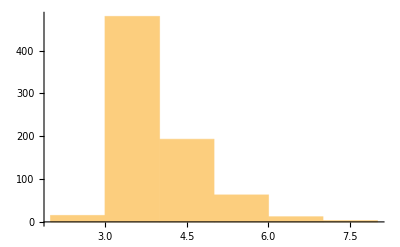

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

### Cube2

```mathematica
{points2,lines2,radius2} = readSkel["data\\cube2\\cube2_skel.ply"];
```

```mathematica
{J2,G2}=initJG[points2,lines2,radius2];
```

Initial graph built!

Basic junctions computed!

47500

47000

46500

46000

45500

45000

44500

44000

43500

43000

42500

42000

41500

41000

40500

40000

39500

39000

38500

38000

37500

37000

36500

36000

35500

35000

34500

34000

33500

33000

32500

32000

31500

31000

30500

30000

29500

29000

28500

28000

27500

27000

26500

26000

25500

25000

24500

24000

23500

23000

22500

22000

21500

21000

20500

20000

19500

19000

18500

18000

17500

17000

16500

16000

15500

15000

14500

14000

13500

13000

12500

12000

11500

11000

10500

10000

9500

9000

8500

8000

7500

7000

6500

6000

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

```mathematica
Export["data\\cube2\\basicJunctions2.xls", J2, "XLS"];
adjMatrix2 = AdjacencyMatrix[G2];
Export["data\\cube2\\adjMatrix2.tgf",adjMatrix2];
```

```mathematica
G22 = Import["data\\cube2\\adjMatrix2.tgf"];
J22 = Import["data\\cube2\\basicJunctions2.xls"];
```

```mathematica
{Jres2,Gres2}=computeCN[J2,G2];
```

{2.10982,1132}

{1.92539,1131}

{1.86569,1130}

{1.86128,1129}

{1.84402,1128}

{1.78151,1127}

{1.71165,1126}

{1.67796,1125}

{1.62293,1124}

{1.61354,1123}

{1.60475,1122}

{1.57963,1121}

{1.57613,1120}

{1.55542,1119}

{1.52972,1118}

{1.48687,1117}

{1.47651,1116}

{1.42553,1115}

{1.42164,1114}

{1.41598,1113}

{1.40339,1112}

{1.3956,1111}

{1.3275,1110}

{1.31004,1109}

{1.27362,1108}

{1.27167,1107}

{1.26578,1106}

{1.25999,1105}

{1.24262,1104}

{1.24066,1103}

{1.2211,1102}

{1.21987,1101}

{1.19359,1100}

{1.19149,1099}

{1.15579,1098}

{1.13219,1097}

{1.13104,1096}

{1.11025,1095}

{1.10965,1094}

{1.10782,1093}

{1.10187,1092}

{1.09961,1091}

{1.09347,1090}

{1.0913,1089}

{1.07837,1088}

{1.07758,1087}

{1.06742,1086}

{1.06725,1085}

{1.0619,1084}

{1.05904,1083}

{1.05481,1082}

{1.05156,1081}

{1.04214,1080}

{1.04213,1079}

{1.03134,1078}

{1.023,1077}

{1.01902,1076}

{1.01821,1075}

{1.00985,1074}

{1.00664,1073}

{1.00503,1072}

{1.00471,1071}

{0.997613,1070}

{0.991665,1069}

{0.99127,1068}

{0.988194,1067}

{0.981332,1066}

{0.981243,1065}

{0.978598,1064}

{0.978348,1063}

{0.957805,1062}

{0.955179,1061}

{0.949519,1060}

{0.942382,1059}

{0.942345,1058}

{0.93932,1057}

{0.933828,1056}

{0.932599,1055}

{0.92504,1054}

{0.921807,1053}

{0.917148,1052}

{0.915694,1051}

{0.913142,1050}

{0.912185,1049}

{0.911193,1048}

{0.910025,1047}

{0.901858,1046}

{0.895127,1045}

{0.894846,1044}

{0.892196,1043}

{0.891022,1042}

{0.886955,1041}

{0.885672,1040}

{0.876926,1039}

{0.87678,1038}

{0.868855,1037}

{0.866945,1036}

{0.861584,1035}

{0.860187,1034}

{0.851726,1033}

{0.828353,1032}

{0.82792,1031}

{0.826345,1030}

{0.823518,1029}

{0.822077,1028}

{0.821286,1027}

{0.817901,1026}

{0.817653,1025}

{0.816087,1024}

{0.815713,1023}

{0.810841,1022}

{0.805179,1021}

{0.801283,1020}

{0.798697,1019}

{0.788527,1018}

{0.787268,1017}

{0.78654,1016}

{0.774741,1015}

{0.772822,1014}

{0.770517,1013}

{0.7701,1012}

{0.766756,1011}

{0.765203,1010}

{0.76454,1009}

{0.762795,1008}

{0.762524,1007}

{0.75632,1006}

{0.753902,1005}

{0.748189,1004}

{0.747118,1003}

{0.746438,1002}

{0.742256,1001}

{0.742208,1000}

{0.741381,999}

{0.740165,998}

{0.73096,997}

{0.715147,996}

{0.712936,995}

{0.707995,994}

{0.707089,993}

{0.700459,992}

{0.699119,991}

{0.68782,990}

{0.686183,989}

{0.683844,988}

{0.679209,987}

{0.678712,986}

{0.678189,985}

{0.676048,984}

{0.673426,983}

{0.66669,982}

{0.666552,981}

{0.663609,980}

{0.65791,979}

{0.654235,978}

{0.651364,977}

{0.64972,976}

{0.647577,975}

{0.643573,974}

{0.641035,973}

{0.639878,972}

{0.636774,971}

{0.635254,970}

{0.632139,969}

{0.626796,968}

{0.625815,967}

{0.625305,966}

{0.623594,965}

{0.623029,964}

{0.622883,963}

{0.619738,962}

{0.618605,961}

{0.617001,960}

{0.612257,959}

{0.60996,958}

{0.608158,957}

{0.603768,956}

{0.591434,955}

{0.583081,954}

{0.577804,953}

{0.572747,952}

{0.572579,951}

{0.571231,950}

{0.570934,949}

{0.570623,948}

{0.569652,947}

{0.569347,946}

{0.566399,945}

{0.565843,944}

{0.559489,943}

{0.559021,942}

{0.55511,941}

{0.554931,940}

{0.547811,939}

{0.545775,938}

{0.544472,937}

{0.54062,936}

{0.534141,935}

{0.530406,934}

{0.52759,933}

{0.524305,932}

{0.523559,931}

{0.511981,930}

{0.509593,929}

{0.509461,928}

{0.501126,927}

{0.499003,926}

{0.489534,925}

{0.486082,924}

{0.485895,923}

{0.481951,922}

{0.472345,921}

{0.468831,920}

{0.465579,919}

{0.462761,918}

{0.460167,917}

{0.455318,916}

{0.450623,915}

{0.445189,914}

{0.443381,913}

{0.441416,912}

{0.440752,911}

{0.43811,910}

{0.437601,909}

{0.437041,908}

{0.431045,907}

{0.428408,906}

{0.426058,905}

{0.425358,904}

{0.417855,903}

{0.417083,902}

{0.414183,901}

{0.411149,900}

{0.394849,899}

{0.393172,898}

{0.390603,897}

{0.384268,896}

{0.372588,895}

{0.364619,894}

{0.361727,893}

{0.358223,892}

{0.35266,891}

{0.344852,890}

{0.340746,889}

{0.330257,888}

{0.328524,887}

{0.326814,886}

{0.325199,885}

{0.324299,884}

{0.319317,883}

{0.314103,882}

{0.306301,881}

{0.299366,880}

{0.293098,879}

{0.288166,878}

{0.281387,877}

{0.28109,876}

{0.279912,875}

{0.277478,874}

{0.271435,873}

{0.265551,872}

{0.259698,871}

{0.259325,870}

{0.258099,869}

{0.251357,868}

{0.249874,867}

{0.244765,866}

{0.244237,865}

{0.241618,864}

{0.24015,863}

{0.231388,862}

{0.208799,861}

{0.205996,860}

{0.203581,859}

{0.200855,858}

{0.178551,857}

{0.170058,856}

{0.169187,855}

{0.16838,854}

{0.156641,853}

{0.156033,852}

{0.151392,851}

{0.140155,850}

{0.137054,849}

{0.13563,848}

{0.129234,847}

{0.125581,846}

{0.119057,845}

{0.118223,844}

{0.115119,843}

{0.108195,842}

{0.102683,841}

{0.101231,840}

{0.0956782,839}

{0.091425,838}

{0.0866169,837}

{0.0764048,836}

{0.0733461,835}

{0.0717192,834}

{0.056934,833}

{0.044218,832}

{0.0324662,831}

{0.0309252,830}

{0.0294235,829}

{0.0278291,828}

{0.0275815,827}

{0.0181248,826}

{0.0142574,825}

{0.0136119,824}

{0.011119,823}

{0.00328745,822}

{0.0010474,821}

{0.000702921,820}

```mathematica
Export["data\\cube2\\mergedJunctions2.xls", Jres2, "XLS"];
adjMatrixRes2 = AdjacencyMatrix[Gres2];
Export["data\\cube2\\adjMatrixRes2.tgf",adjMatrixRes2];
```

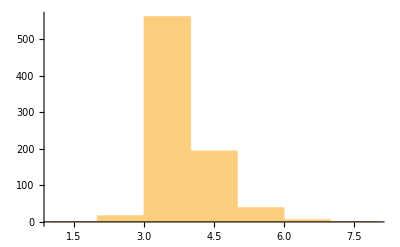

```mathematica
CNs2 = Jres2⟦;;,2⟧;
Histogram[CNs2]
```

#### Visualization

```mathematica
J2=Import["data\\cube2\\basicJunctions2.xls"]⟦1⟧;
J2=ToExpression[J2];
J2⟦;;,4⟧=coordsAlign[J2⟦;;,4⟧,points2];
```

```mathematica
cube2BasicBalls=Table[{Ball[J2⟦i,4⟧,J2⟦i,5⟧]},{i,Dimensions[J2]⟦1⟧}];
```

```mathematica
Jres2=Import["data\\cube2\\mergedJunctions2.xls"]⟦1⟧;
Jres2=ToExpression[Jres2];
Jres2⟦;;,4⟧=coordsAlign[Jres2⟦;;,4⟧,points2];
```

```mathematica
cube2JunctionBalls=Table[{Ball[Jres2⟦i,4⟧,Jres2⟦i,5⟧]},{i,Dimensions[Jres2]⟦1⟧}];
```

```mathematica
Show[Graphics3D[{skelCube2,{Opacity[0.5],Blue,cube2JunctionBalls},{Opacity[0.5],Red,cube2BasicBalls}}]]
```

-Graphics3D-

### Cube3

```mathematica
{points3,lines3,radius3} = readSkel["data\\cube3\\cube3_skel.ply"];
```

```mathematica
{J3,G3}=initJG[points3,lines3,radius3];
```

Initial graph built!

Basic junctions computed!

47000

46500

46000

45500

45000

44500

44000

43500

43000

42500

42000

41500

41000

40500

40000

39500

39000

38500

38000

37500

37000

36500

36000

35500

35000

34500

34000

33500

33000

32500

32000

31500

31000

30500

30000

29500

29000

28500

28000

27500

27000

26500

26000

25500

25000

24500

24000

23500

23000

22500

22000

21500

21000

20500

20000

19500

19000

18500

18000

17500

17000

16500

16000

15500

15000

14500

14000

13500

13000

12500

12000

11500

11000

10500

10000

9500

9000

8500

8000

7500

7000

6500

6000

5500

5000

4500

4000

3500

3000

2500

2000

1500

1000

500

0

simplified graph done!

```mathematica
Export["data\\cube3\\basicJunctions3.xls", J3, "XLS"];
adjMatrix3 = AdjacencyMatrix[G3];
```

```mathematica
Export["data\\cube3\\adjMatrix3.tgf",adjMatrix3];
```

```mathematica
{Jres3,Gres3}=computeCN[J3,G3];
```

{2.56148,4703}

{2.24432,4702}

{2.0065,4701}

{1.80916,4700}

{1.74453,4699}

{1.64396,4698}

{1.62069,4697}

{1.60871,4696}

{1.59771,4695}

{1.51563,4694}

{1.50802,4693}

{1.49951,4692}

{1.42442,4691}

{1.42319,4690}

{1.39453,4689}

{1.38616,4688}

{1.37501,4687}

{1.36454,4686}

{1.3645,4685}

{1.34392,4684}

{1.31059,4683}

{1.29791,4682}

{1.29766,4681}

{1.27802,4680}

{1.26108,4679}

{1.23871,4678}

{1.23868,4677}

{1.22915,4676}

{1.20249,4675}

{1.17582,4674}

{1.15961,4673}

{1.13231,4672}

{1.1312,4671}

{1.11374,4670}

{1.10529,4669}

{1.104,4668}

{1.10351,4667}

{1.09941,4666}

{1.08414,4665}

{1.07714,4664}

{1.07381,4663}

{1.06829,4662}

{1.06264,4661}

{1.05846,4660}

{1.04174,4659}

{1.01916,4658}

{1.01082,4657}

{0.997745,4656}

{0.984127,4655}

{0.978796,4654}

{0.977312,4653}

{0.972894,4652}

{0.969265,4651}

{0.968478,4650}

{0.967173,4649}

{0.963945,4648}

{0.963485,4647}

{0.961721,4646}

{0.960928,4645}

{0.960138,4644}

{0.959971,4643}

{0.954766,4642}

{0.953871,4641}

{0.952868,4640}

{0.950964,4639}

{0.946041,4638}

{0.944809,4637}

{0.927805,4636}

{0.926511,4635}

{0.926445,4634}

{0.920748,4633}

{0.920468,4632}

{0.909949,4631}

{0.904307,4630}

{0.890807,4629}

{0.888877,4628}

{0.883448,4627}

{0.881352,4626}

{0.879396,4625}

{0.878268,4624}

{0.877614,4623}

{0.877448,4622}

{0.87351,4621}

{0.871462,4620}

{0.869347,4619}

{0.867118,4618}

{0.859408,4617}

{0.857776,4616}

{0.854355,4615}

{0.852667,4614}

{0.845157,4613}

{0.842568,4612}

{0.842052,4611}

{0.836636,4610}

{0.836082,4609}

{0.835181,4608}

{0.82866,4607}

{0.826341,4606}

{0.822519,4605}

{0.819132,4604}

{0.814356,4603}

{0.810241,4602}

{0.809275,4601}

{0.79878,4600}

{0.794403,4599}

{0.793506,4598}

{0.792898,4597}

{0.790381,4596}

{0.788378,4595}

{0.785616,4594}

{0.785469,4593}

{0.782503,4592}

{0.779882,4591}

{0.778927,4590}

{0.778202,4589}

{0.776764,4588}

{0.771813,4587}

{0.771247,4586}

{0.762147,4585}

{0.758911,4584}

{0.757228,4583}

{0.757114,4582}

{0.756353,4581}

{0.756336,4580}

{0.754952,4579}

{0.754912,4578}

{0.747385,4577}

{0.744915,4576}

{0.742903,4575}

{0.737708,4574}

{0.735021,4573}

{0.731757,4572}

{0.731204,4571}

{0.729467,4570}

{0.728931,4569}

{0.724246,4568}

{0.723601,4567}

{0.718983,4566}

{0.71834,4565}

{0.717262,4564}

{0.711325,4563}

{0.710502,4562}

{0.708617,4561}

{0.706545,4560}

{0.703898,4559}

{0.703812,4558}

{0.703183,4557}

{0.701667,4556}

{0.697561,4555}

{0.69497,4554}

{0.693857,4553}

{0.685604,4552}

{0.685424,4551}

{0.684113,4550}

{0.683898,4549}

{0.681765,4548}

{0.680299,4547}

{0.678063,4546}

{0.676526,4545}

{0.675566,4544}

{0.669639,4543}

{0.667466,4542}

{0.667077,4541}

{0.660072,4540}

{0.659657,4539}

{0.659608,4538}

{0.65839,4537}

{0.656474,4536}

{0.655025,4535}

{0.65228,4534}

{0.647232,4533}

{0.645387,4532}

{0.642407,4531}

{0.641645,4530}

{0.641474,4529}

{0.641221,4528}

{0.640921,4527}

{0.635467,4526}

{0.635425,4525}

{0.632139,4524}

{0.629063,4523}

{0.62687,4522}

{0.625423,4521}

{0.622781,4520}

{0.621586,4519}

{0.621221,4518}

{0.619057,4517}

{0.618709,4516}

{0.61771,4515}

{0.615048,4514}

{0.613584,4513}

{0.612879,4512}

{0.609498,4511}

{0.608335,4510}

{0.604661,4509}

{0.603222,4508}

{0.601619,4507}

{0.601286,4506}

{0.598621,4505}

{0.592528,4504}

{0.591381,4503}

{0.59049,4502}

{0.590052,4501}

{0.589049,4500}

{0.588772,4499}

{0.581662,4498}

{0.580746,4497}

{0.580383,4496}

{0.579139,4495}

{0.576955,4494}

{0.572682,4493}

{0.567047,4492}

{0.566486,4491}

{0.564947,4490}

{0.561006,4489}

{0.560978,4488}

{0.560477,4487}

{0.552369,4486}

{0.548039,4485}

{0.54636,4484}

{0.54064,4483}

{0.537512,4482}

{0.536716,4481}

{0.532008,4480}

{0.528595,4479}

{0.524822,4478}

{0.523962,4477}

{0.514531,4476}

{0.512622,4475}

{0.50817,4474}

{0.50737,4473}

{0.507367,4472}

{0.50586,4471}

{0.505531,4470}

{0.500577,4469}

{0.499982,4468}

{0.498985,4467}

{0.498928,4466}

{0.497644,4465}

{0.495743,4464}

{0.495397,4463}

{0.494647,4462}

{0.487856,4461}

{0.487056,4460}

{0.482049,4459}

{0.479705,4458}

{0.47827,4457}

{0.47514,4456}

{0.472603,4455}

{0.468945,4454}

{0.466701,4453}

{0.462882,4452}

{0.449252,4451}

{0.44698,4450}

{0.446068,4449}

{0.439686,4448}

{0.439303,4447}

{0.436104,4446}

{0.433504,4445}

{0.431016,4444}

{0.42703,4443}

{0.425392,4442}

{0.42405,4441}

{0.423576,4440}

{0.423367,4439}

{0.41852,4438}

{0.415988,4437}

{0.408142,4436}

{0.406755,4435}

{0.403529,4434}

{0.400772,4433}

{0.384726,4432}

{0.384395,4431}

{0.381269,4430}

{0.377612,4429}

{0.376214,4428}

{0.374857,4427}

{0.373025,4426}

{0.371378,4425}

{0.37104,4424}

{0.368749,4423}

{0.357934,4422}

{0.350718,4421}

{0.349034,4420}

{0.347865,4419}

{0.347123,4418}

{0.346541,4417}

{0.345299,4416}

{0.34323,4415}

{0.339918,4414}

{0.332642,4413}

{0.329065,4412}

{0.328998,4411}

{0.328962,4410}

{0.326871,4409}

{0.313286,4408}

{0.312045,4407}

{0.31049,4406}

{0.306713,4405}

{0.305407,4404}

{0.301191,4403}

{0.298454,4402}

{0.298008,4401}

{0.293098,4400}

{0.291575,4399}

{0.289862,4398}

{0.285078,4397}

{0.283762,4396}

{0.281533,4395}

{0.272429,4394}

{0.272202,4393}

{0.272128,4392}

{0.267606,4391}

{0.264534,4390}

{0.261691,4389}

{0.261472,4388}

{0.258943,4387}

{0.257107,4386}

{0.252473,4385}

{0.250684,4384}

{0.249902,4383}

{0.247524,4382}

{0.243974,4381}

{0.22872,4380}

{0.228654,4379}

{0.227632,4378}

{0.227566,4377}

{0.212969,4376}

{0.211819,4375}

{0.19241,4374}

{0.190514,4373}

{0.188284,4372}

{0.182538,4371}

{0.179207,4370}

{0.179125,4369}

{0.17827,4368}

{0.17779,4367}

{0.170395,4366}

{0.169062,4365}

{0.169017,4364}

{0.164755,4363}

{0.160138,4362}

{0.159854,4361}

{0.153822,4360}

{0.150192,4359}

{0.148268,4358}

{0.143133,4357}

{0.141938,4356}

{0.14146,4355}

{0.130896,4354}

{0.130436,4353}

{0.127206,4352}

{0.127014,4351}

{0.124709,4350}

{0.122756,4349}

{0.113361,4348}

{0.112565,4347}

{0.10545,4346}

{0.0973204,4345}

{0.0958621,4344}

{0.0951897,4343}

{0.0889528,4342}

{0.0860667,4341}

{0.0850316,4340}

{0.0832754,4339}

{0.0801909,4338}

{0.0728761,4337}

{0.0714581,4336}

{0.0681063,4335}

{0.0675177,4334}

{0.0648442,4333}

{0.0638921,4332}

{0.0523803,4331}

{0.0453552,4330}

{0.0423726,4329}

{0.0422406,4328}

{0.0305112,4327}

{0.0297429,4326}

{0.028997,4325}

{0.0268221,4324}

{0.0257839,4323}

{0.0238635,4322}

{0.0182198,4321}

{0.0174594,4320}

{0.00439003,4319}

```mathematica
Export["data\\cube3\\mergedJunctions3.xls", Jres3, "XLS"];
adjMatrixRes3 = AdjacencyMatrix[Gres3];
```

```mathematica
Export["data\\cube3\\adjMatrixRes3.tgf",adjMatrixRes3];
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,4,4,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,5,5,4,5,4,4,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,2,4,4,4,4,4,4,4,4,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,4,4,4,4,4,4,4,5,4,4,4,4,4,5,4,4,4,4,4,4,4,4,2,2,2,4,4,4,4,2,4,5,2,4,5,4,2,5,4,4,5,4,4,4,4,4,4,4,4,4,4,2,4,5,4,4,4,5,4,4,5,4,4,5,4,4,4,5,4,5,5,4,4,5,2,5,1,4,4,4,4,4,4,4,4,4,4,2,4,4,4,5,5,6,4,4,6,4,4,4,4,4,5,4,5,2,2,5,4,4,2,4,4,4,4,6,4,4,3,4,4,5,4,2,5,4,4,4,2,4,4,5,4,4,4,5,4,5,2,5,5,4,4,4,4,4,4,4,1,5,6,4,4,6,4,4,4,4,4,6,4,4,4,4,3,5,5,4,4,4,2,4,5,4,5,2,6,4,3,4,4,4,5,2,4,5,4,3,8,6,4,6,5,5,5,4,4,5,5,4,5,4,4,4,4,5,4,4,2,4,5,4,7,5,4,8,4,14244}

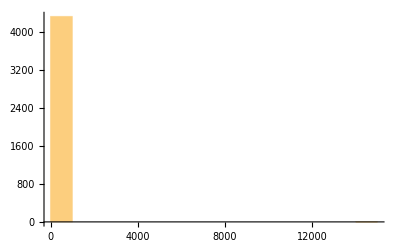

```mathematica
CNs = Jres3⟦;;,2⟧
Histogram[CNs]
```

#### Visualization

```mathematica
J3=Import["data\\cube3\\basicJunctions3.xls"]⟦1⟧;
J3=ToExpression[J3];
J3⟦;;,4⟧=coordsAlign[J3⟦;;,4⟧,points3];
```

```mathematica
cube3BasicBalls=Table[{Ball[J3⟦i,4⟧,J3⟦i,5⟧]},{i,Dimensions[J3]⟦1⟧}];
```

```mathematica
Jres3=Import["data\\cube3\\mergedJunctions3.xls"]⟦1⟧;
Jres3=ToExpression[Jres3];
Jres3⟦;;,4⟧=coordsAlign[Jres3⟦;;,4⟧,points3];
```

```mathematica
cube3JunctionBalls=Table[{Ball[Jres3⟦i,4⟧,Jres3⟦i,5⟧]},{i,Dimensions[Jres3]⟦1⟧}];
```

```mathematica
Show[Graphics3D[{skelCube3,{Opacity[0.5],Blue,cube3JunctionBalls},{Opacity[0.5],Red,cube3BasicBalls}}]]
```

-Graphics3D-

### Cube4

```mathematica
{points4,lines4,radius4} = readSkel["data\\cube4\\cube4_skel.ply"];
```

```mathematica
{J4,G4}=initJG[points4,lines4,radius4];
```

```mathematica
Export["basicJunctions4.xls", J4, "XLS"];
adjMatrix4 = AdjacencyMatrix[G4];
Export["adjMatrix4.xls",adjMatrix4,"XLS"];
```

```mathematica
{Jres4,Gres4}=computeCN[J4,G4];
```

```mathematica
Export["mergedJunctions4.xls", Jres4, "XLS"];
adjMatrixRes4 = AdjacencyMatrix[Gres4];
Export["adjMatrixRes4.xls",adjMatrixRes4,"XLS"];
```

```mathematica
CNs = Jres1⟦;;,2⟧;
Histogram[CNs]
```

#### Visualization

```mathematica
Jres4=Import[]
```

```mathematica
cube4JunctionBalls=
```

## Real-World Data Test & Visualization

### scoba12_Small

```mathematica
maGraphic = Import["scoba12_small.ply","Graphics3D"];
skelGraphic = Import["scoba12_small_skel.ply","Graphics3D"];
```

```mathematica
Show[Graphics3D[{edgeInCoords}], maGraphic]
```

-Graphics3D-

```mathematica
Show[skelGraphic, maGraphic]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{edgeInCoords,{Opacity[0.5],Blue,junctionBalls}}]]
```